{0.570038,0.0208685}

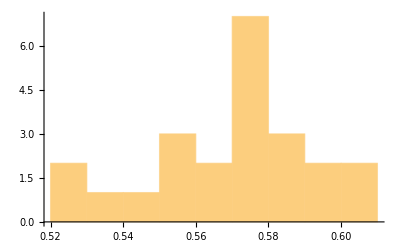

```mathematica
depthlist = {0.6, 0.571428571,0.580952381,0.566037736,0.58490566,0.575471698,0.566037736,0.594339623,0.556603774, 0.603773585, 0.575471698, 0.58490566, 0.556603774, 0.556603774, 0.575471698, 0.547169811, 0.575471698, 0.594339623, 0.575471698, 0.528301887, 0.575471698, 0.528301887, 0.537735849};
avg = Mean[depthlist];
deviationSq = Map[(#-avg)^2&, depthlist];
err = Sqrt[Sum[deviationSq[[i]],{i,1,Length[depthlist]}]/(Length[depthlist]-1)];
depth = {avg, err}
Histogram[depthlist,7]
```

```mathematica
nn = (2*0.063)/(2/(6*10^23));
N0 = 532;
elScat = {27, N[Sqrt[27*(1-27/N0)]], "elastic"}
inelScat = {64, N[Sqrt[64*(1-64/N0)]], "inelastic"}
totalScat = {91, N[Sqrt[91*(1-91/N0)]], "total"}
L = {174.5*0.852375,Sqrt[(0.1*0.852375)^2 + (174.5*0.00264)^2]};
elCS = {σ[L[[1]],N0,elScat[[1]]]*10^27,Sqrt[D[σ[x,n0,nx],{x,1}]^2*L[[2]]^2 +D[σ[x,n0,nx],{nx,1}]^2*elScat[[2]]^2  ]*10^27, "Elastic cross section and error in mb"}/.{x->L[[1]],n0->N0, nx -> elScat[[1]]}
totalCS = {σ[L[[1]],N0,totalScat[[1]]]*10^27,Sqrt[D[σ[x,n0,nx],{x,1}]^2*L[[2]]^2 +D[σ[x,n0,nx],{nx,1}]^2*totalScat[[2]]^2  ]*10^27, "Total cross section and error in mb"}/.{x->L[[1]],n0->N0, nx ->( elScat[[1]]+inelScat[[1]])}
```

{27,5.06258,elastic}

{64,7.50338,inelastic}

{91,8.68529,total}

{9.26393,1.78328,Elastic cross section and error in mb}

{33.3666,3.50448,Total cross section and error in mb}

```mathematica
nn = (2*0.063)/(2/(6*10^23));
N02 = 297;
as = {N[Sqrt[8*(1-8/N02)]], 
N[Sqrt[37*(1-37/N02)]]};
elScat2 = {8, 3}
inelScat2 = {37,6 }
tot = {45, 6}
σ[x_, n0_, nx_] = Log[n0/(n0-nx)]/(nn*x);
L2 = {99.56,0.04};
elCS2 = {σ[L2[[1]],N02,elScat2[[1]]]*10^27,Sqrt[D[σ[x,n0,nx],{x,1}]^2*L2[[2]]^2 +D[σ[x,n0,nx],{nx,1}]^2*elScat2[[2]]^2  ]*10^27, "GERMAN PDF Elastic cross section and error in mb"}/.{x->L[[1]],n0->N02, nx -> elScat2[[1]]}
totalCS2 = {σ[L2[[1]],N02,tot[[1]]]*10^27,Sqrt[D[σ[x,n0,nx],{x,1}]^2*L2[[2]]^2 +D[σ[x,n0,nx],{nx,1}]^2*tot[[2]]^2 ]*10^27, "GERMAN PDF Total cross section and error in mb"}/.{x->L2[[1]],n0->N02, nx ->( elScat2[[1]]+inelScat2[[1]])}
```

{8,3}

{37,6}

{45,6}

{7.25559,1.84631,GERMAN PDF Elastic cross section and error in mb}

{43.6585,6.32668,GERMAN PDF Total cross section and error in mb}